```mathematica
ℏ=1.0*10^-34;
kb=1.38*10^-23;
T0=6.4*10^-6;
m171=170.936*(1.660539*10^-27);
```

```mathematica
ωt=2π* 67.*10.^3;
```

```mathematica
Pn[n_,T_]:=E^(-ℏ ωt n/(kb T))(1-E^(-ℏ ωt/(kb T)))
T[nbar_]:=(ℏ ωt)/(kb Log[1/nbar+1])
```

## H form

```mathematica
n0=2;
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
MatrixForm[a];
For[i=n0,i>0n0,i--,
a[[{i,i+1}]]=a[[{i+1,i}]];
]
MatrixForm[a];
MatrixForm[a†];
σ=({{0, 0}, {1, 0}});
```

```mathematica
Hr=KroneckerProduct[Ω/2(IdentityMatrix[n0+1]+Sum[1/(n!)(I η)^n MatrixPower[a+a†,n],{n,1,n0}]),σ†];
HR=Hr+Hr†;
MatrixForm[HR];
```

```mathematica
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ω, 0}, {0, ω}})];
H=Hs+Hm+HR;
MatrixForm[H];
```

```mathematica
nbar=0.5;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π 67.*10^3;
Ωr=2π 2*10^4;
Ttot=15*(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0]]=1-Sum[Pns[[n]],{n,1,n0-1}]
```

0.0000508053

```mathematica
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.967866,{t→0.00045309}}

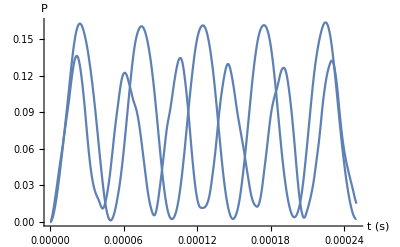

```mathematica
Plot[Table[Evaluate[ρ[t]/.ρs][[1,n,n]],{n,2*n0-1,2*n0+1,2}],{t,0,Ttot},PlotRange->All,PlotLegends->{},AxesLabel->{"t (s)","P"}]
```

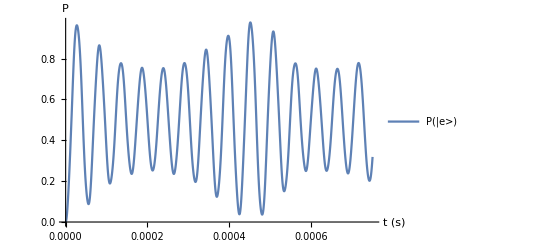

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},PlotLegends->{"P(|e>)"},AxesLabel->{"t (s)","P"}]
```

### get the pi pulse fidelity for a given Ωr and ωt

```mathematica
Ωr=2π 2.*10^4;
Ttot=(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
```

```mathematica
ωt=2π 67*10.^3;
E0=1/2 ℏ ωt;
v0=√((2E0)/m171);
fdopp=1/(2π)v0*k
```

30976.1

#### vary trap freq

```mathematica
nbars=Table[i*0.2,{i,1,5}];
numGrid=50;
ωts=2π Subdivide[2.*10^3,2.*10^5,numGrid-1];
piFidelities=Table[{ωts[[i]]/(2π)*10^-3,0},{j,1,Length[nbars]},{i,1,numGrid}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
For[ii=1,ii≤numGrid,ii++,
ωt =ωts[[ii]];
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,ii,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
Print[jj]
]
```

1

2

3

4

5

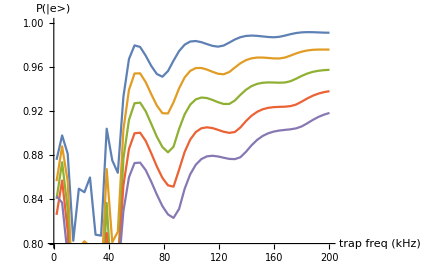

```mathematica
ListPlot[{piFidelities[[1]],piFidelities[[2]],piFidelities[[3]],piFidelities[[4]],piFidelities[[5]]},Joined->True,PlotRange->{0.8,1.0},AxesLabel->{"trap freq (kHz)", "P(|e>)"}]
```

#### vary temp

```mathematica
numTs=100;
nbars=Table[i*0.05,{i,1,numTs}];
ωt=2π 67.*10^3;
piFidelities=Table[{nbars[[i]],0},{i,1,Length[nbars]}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
```

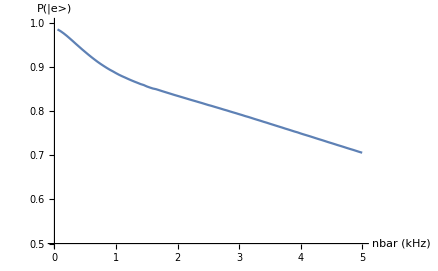

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.0},AxesLabel->{"nbar (kHz)", "P(|e>)"}]
```

#### raman rabi freq

```mathematica
numTs=30;
nbar=0.1;
ωt=2π 67.*10^3;
Ωrs=Table[2π *i*20.*10^3,{i,1,numTs}];
piFidelities=Table[{Ωrs[[i]]*10^-3/(2π),0},{i,1,Length[Ωrs]}];
```

```mathematica
For[jj=1,jj≤Length[Ωrs],jj++,
ωR=(ℏ k^2)/(2 m171);
Ωr=Ωrs[[jj]];
Ttot=(2π)/Ωr;
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
];
```

$Aborted

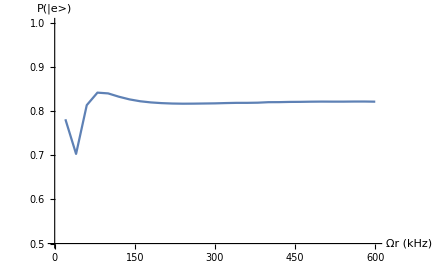

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.0},AxesLabel->{"Ωr (kHz)", "P(|e>)"}]
```

## no η expansion

```mathematica
ClearAll["Global`*"]
```

```mathematica
n0=8;
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
For[i=n0,i>0n0,i--,
a[[{i,i+1}]]=a[[{i+1,i}]];
]
σ=({{0, 0}, {1, 0}});
```

```mathematica
Hr=KroneckerProduct[Ω/2 MatrixExp[I η (a+a†)],σ†];
HR=Hr+Hr†;
MatrixForm[HR];
```

```mathematica
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ω, 0}, {0, ω}})];
H=Hs+Hm+HR;
MatrixForm[H];
```

(1)
 |  |  |  |

```mathematica
nbar=0.5;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π 67.*10^3;
Ωr=2π 2*10^4;
Ttot=10*(2π)/Ωr;
k=√2(2π)/(556.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt);
Pns[[n0]]=1-Sum[Pns[[n]],{n,1,n0-1}]
```

0.000457247

```mathematica
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(30 Ωr)}];
NMaximize[{ρi[t],{t>0.,t<Ttot}},t]
```

{0.96782,{t→0.000449432}}

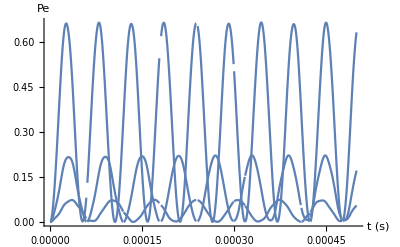

```mathematica
Plot[Table[Evaluate[ρ[t]/.ρs][[1,n,n]],{n,2n0-3,2*n0+1,2}],{t,0,Ttot},PlotRange->All,PlotLegends->{},AxesLabel->{"t (s)","Pe"}]
```

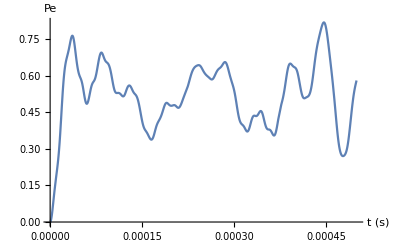

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,2*n0+1,2}],{t,0,Ttot},AxesLabel->{"t (s)","Pe"}]
```

#### raman rabi freq

```mathematica
numTs=40;
nbar=0.1;
ωt=2π 130.*10^3;
Ωrs=Table[2π *i*2.*10^3,{i,1,numTs}];
piFidelities=Table[{Ωrs[[i]]*10^-3/(2π),0},{i,1,Length[Ωrs]}];
```

```mathematica
For[jj=1,jj≤Length[Ωrs],jj++,
ωR=(ℏ k^2)/(2 m171);
Ωr=Ωrs[[jj]];
Ttot=(1.5π)/Ωr;
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(40 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
If[Mod[jj,5]==0,Print[jj]]
];
```

5

10

15

20

25

30

35

40

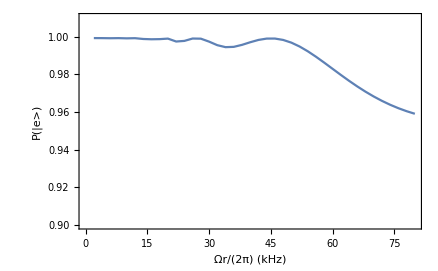

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.9,1.01},BaseStyle->{FontSize->13},Frame->True,FrameLabel->{"Ωr/(2π) (kHz)", "P(|e>)"}]
```

```mathematica
η0
```

0.423101

#### temperature

```mathematica
num=25;
nbars=Table[0.5*i,{i,1,num}];
ωt=2π 67.*10^3;
Ωr=2π 20.*10^3;
piFidelities=Table[{nbars[[i]],0},{i,1,Length[nbars]}];
```

```mathematica
For[jj=1,jj≤Length[nbars],jj++,
ωR=(ℏ k^2)/(2 m171);
Ttot=(1.5π)/Ωr;
η0=√(ωR/ωt);
T0=(ℏ ωt)/(kb Log[1/nbars[[jj]]+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(40 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
If[Mod[jj,5]==0,Print[jj]]
];
```

5

10

15

20

25

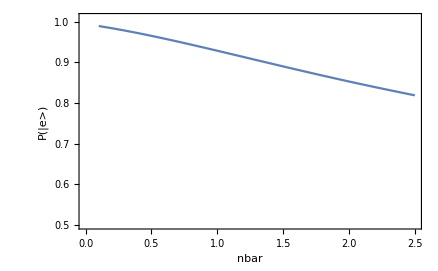

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.5,1.01},BaseStyle->{FontSize->13},Frame->True,FrameLabel->{"nbar", "P(|e>)"}]
```

```mathematica
η0
```

0.423101

#### eta

```mathematica
numTs=20;
nbar=0.1;
ωt=2π 40.*10^3;
Ωr=2π 10^5;
θs=Table[5*π/180*i,{i,0,18}];
η0s=Table[√(2(1-Cos[θs[[i]]]))√(ωR/ωt),{i,1, Length[θs]}];
piFidelities=Table[{θs[[i]]*180/π,0},{i,1,Length[θs]}];
```

```mathematica
For[jj=1,jj≤Length[θs],jj++,
ωR=(ℏ k^2)/(2 m171);
Ttot=(1.5π)/Ωr;
η0=η0s[[jj]];
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
Hn=H/.{ω->ωt,Ω->Ωr,δ->0,η->η0};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->7];
ρi=Interpolation@Table[{t,Sum[Abs[Evaluate[ρ[t] /. ρs][[1,i,i]]], {i, 1,2*n0+1, 2}]},{t,0.,Ttot,π/(40 Ωr)}];
piFidelities[[jj,2]]=NMaximize[{ρi[t],{t>0.,t<Ttot}},t][[1]];
If[Mod[jj,5]==0,Print[jj]]
];
```

5

10

15

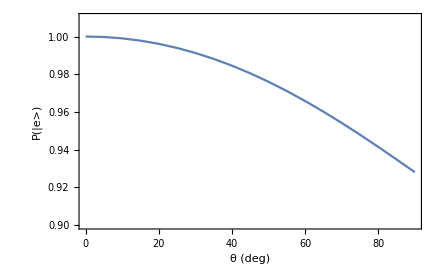

```mathematica
ListPlot[piFidelities,Joined->True,PlotRange->{0.9,1.01},BaseStyle->{FontSize->13},Frame->True,FrameLabel->{"θ (deg)", "P(|e>)"}]
```

## 3 level

```mathematica
n0=7;
a=DiagonalMatrix[Table[√(n0-n),{n,0,n0}]];
For[i=n0,i>0n0,i--,
a[[{i,i+1}]]=a[[{i+1,i}]];
]
σ=({{0, 0}, {1, 0}});
```

```mathematica
Hr=KroneckerProduct[Ω/2 MatrixExp[I η (a+a†)],σ†];
HR=Hr+Hr†;
MatrixForm[HR];
```

```mathematica
Hs0=({{-1/2 δ, 0}, {0, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],({{ω, 0}, {0, ω}})];
H=Hs+Hm+HR;
MatrixForm[H];
```

```mathematica
Hs0=({{0, Ω1/2, Ω2/2}, {Ω1/2, δ1, 0}, {Ω2/2, 0, δ2}});
```

```mathematica
nbar=0.1;
T0=(ℏ ωt)/(kb Log[1/nbar+1]);
Pns=Table[Pn[n,T0],{n,0,n0}];
ωt=2π 67.*10^3;
Δ=2π 160.*10^6;
Ω10=√(2π 2*10^4*(2*Δ));
Ω20=√(2π 2*10^4*(2*Δ));
Ttot=1/(20.*10^3);
```

```mathematica
Hn=Hs0/.{Ω2->Ω20,Ω1->Ω10,δ1->-Δ,δ2->-Δ};
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn,ρ[0]==DiagonalMatrix[{0,0,1}]},ρ,{t,0,Ttot},AccuracyGoal->7];
```

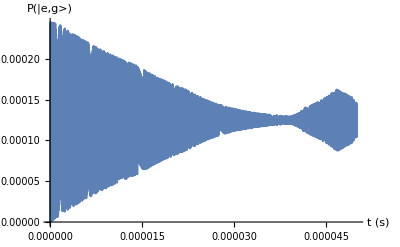

```mathematica
Plot[Evaluate[ρ[t] /. ρs][[1,1]],{t,0,Ttot},AxesLabel->{"t (s)", "P(|e,g>)"}]
```

## quantization axes

```mathematica
muB=9.274010078*10^-24;
ℏ=1.*10^-34;
gl=1;
gs=2;
gj[j_,s_,l_]:=gl (j(j+1)-s(s+1)+l(l+1))/(2 j(j+1))+gs (j(j+1)+s(s+1)-l(l+1))/(2 j(j+1));
gf[j_,s_,l_,f_,i_]:=gj[j,s,l] (f(f+1)-i(i+1)+j(j+1))/(2 f(f+1));
```

```mathematica
gf[1,1,1,3/2,1/2]
```

1

```mathematica
Fx=1/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}});
Fy=1/(2 I)({{0, √3, 0, 0}, {-√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, -√3, 0}});
Fz=({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}});
Hb=muB/(2π ℏ)gf[1,1,1,3/2,1/2] (Bx Fx + By Fy + Bz Fz);
MatrixForm[Hb];
```

```mathematica
Itweezer=(2*P0)/(π w0^2);
He=-1/4(10^-4)Itweezer*(αs IdentityMatrix[4]+αt 2/3(Sin[θ]^2 Fy.Fy+Cos[θ]^2 Fz.Fz));
H=He;
MatrixForm[H]
```

(-(P0 (αs+2/3 αt ((9 Cos[θ]^2)/4+(3 Sin[θ]^2)/4)))/(20000 π w0^2) | 0 | (P0 αt Sin[θ]^2)/(20000 √3 π w0^2) | 0
0 | -(P0 (αs+2/3 αt (Cos[θ]^2/4-Sin[θ]^2/4)))/(20000 π w0^2) | 0 | (P0 αt Sin[θ]^2)/(20000 √3 π w0^2)
-(P0 αt Sin[θ]^2)/(20000 √3 π w0^2) | 0 | -(P0 (αs+2/3 αt (Cos[θ]^2/4-Sin[θ]^2/4)))/(20000 π w0^2) | 0
0 | -(P0 αt Sin[θ]^2)/(20000 √3 π w0^2) | 0 | -(P0 (αs+2/3 αt ((9 Cos[θ]^2)/4+(3 Sin[θ]^2)/4)))/(20000 π w0^2))

```mathematica
FullSimplify[H†==H, Assumptions->{P0∈Reals,ω0∈Reals,Bx∈Reals,By∈Reals,Bz∈Reals,w0∈Reals,αs∈Reals,αt∈Reals,P0∈Reals}]
```

{{(P0 αt (Cos[2 θ]-Cos[2 Conjugate[θ]]))/(40000 π w0^2),0,-(P0 αt (Sin[θ]^2+Sin[Conjugate[θ]]^2))/(20000 √3 π w0^2),0},{0,(P0 αt (Cos[2 θ]-Cos[2 Conjugate[θ]]))/(120000 π w0^2),0,-(P0 αt (Sin[θ]^2+Sin[Conjugate[θ]]^2))/(20000 √3 π w0^2)},{(P0 αt (Sin[θ]^2+Sin[Conjugate[θ]]^2))/(20000 √3 π w0^2),0,(P0 αt (Cos[2 θ]-Cos[2 Conjugate[θ]]))/(120000 π w0^2),0},{0,(P0 αt (Sin[θ]^2+Sin[Conjugate[θ]]^2))/(20000 √3 π w0^2),0,(P0 αt (Cos[2 θ]-Cos[2 Conjugate[θ]]))/(40000 π w0^2)}}=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Hn=H/.{αs->-22.4,αt->7.6,P0->0.006,w0->460.*10^-9,Bx->0,By->0,Bz->0.*10^-4};
Eigensystem[Hn]
```

{{6.10746×10^6,6.10746×10^6,1.53439×10^6,1.53439×10^6},{{0.,0.,1.,0.},{0.,0.755929,0.,-0.654654},{0.755929,0.,0.654654,0.},{0.,0.,0.,1.}}}

```mathematica
Eigenvalues[Hn]
```

{6.10746×10^6,6.10746×10^6,1.53439×10^6,1.53439×10^6}

```mathematica
1./(240-12)/(1/(240+14))
```

1.11404

## light shift and rabi difference

```mathematica
Δ0=2π 240.*10^6;
Δ1=Δ0-2π 42.*10^6;
Δ2=Δ0-2π 14.*10^6;
Δ3=Δ0+2π 16.*10^6;
Δ4=Δ0+2π 48.*10^6;
Ωr=2π 150.*10^3;
Ω0=√(Ωr*(2Δ0));
Ωr1=Ωr*Δ0/Δ1;
Ωr2=Ωr*Δ0/Δ2;
(Ωr1-Ωr2)/(2π)
```

22526.1

```mathematica
ωls1=Ωr^2/(4Δ1);
ωls2=Ωr^2/(4Δ2);
ωls1/(2π)
ωls2/(2π)
```

133.929

401.786

```mathematica
(ωls1-ωls2)/(2π)
```

-267.857

```mathematica
Δ0=2π 240.*10^6;
Δ1=2π 42.*10^6;
Δ2=2π 14.*10^6;
Δ3=2π 16.*10^6;
Δ4=2π 48.*10^6;
Δ1p=Δ0-Δ1*0.2;
Δ2p=Δ0-Δ2*0.2;
Δ3p=Δ0+Δ3*0.2;
Δ4p=Δ0+Δ4*0.2;
Ωr=2π 150.*10^3;
Ω0=√(Ωr*(2Δ0));
Ωr1=Ωr*Δ0/Δ1p;
Ωr2=Ωr*Δ0/Δ2p;
(Ωr1-Ωr2)/(2π)
```

3669.76